# Congruent Triangles

### Author

Eric W. Weisstein
August 12, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/Triangles/CongruentTriangles.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/CongruentTriangles.html.

©2026 Wolfram Research, Inc. except for portions noted otherwise

## Illustration

The second triangle is a rotated and translated copy of the first, and matching tick marks identify equal corresponding side lengths.

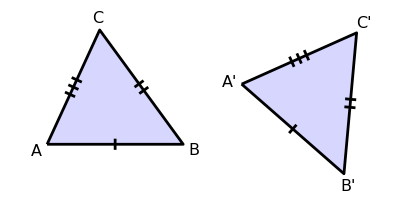

```mathematica
Module[{color, labelPositions, labels1, labels2, neutral, tickMarks, triangle1, 
   triangle2}, triangle1 = {{-2.4, -0.8}, {-0.2, -0.8}, {-1.55, 1.05}}; 
   triangle2 = (RotationTransform[-0.72, Mean[triangle1]][#1] + {3.3, 0.15} & ) /@ triangle1; 
   color = Blue; neutral = LightDarkSwitched[Black, White]; labelPositions[triangle_] := 
    (#1 + 0.2*Normalize[#1 - Mean[triangle]] & ) /@ triangle; 
   tickMarks[p_, q_, n_] := Module[{midpoint, normal, tangent}, 
     midpoint = (p + q)/2; tangent = Normalize[q - p]; normal = {-tangent[[2]], tangent[[1]]}; 
      Table[Line[{midpoint + 0.13*(k - (n + 1)/2)*tangent - 0.09*normal, 
         midpoint + 0.13*(k - (n + 1)/2)*tangent + 0.09*normal}], {k, n}]]; 
   labels1 = {"A", "B", "C"}; labels2 = {"A'", "B'", "C'"}; 
   Graphics[{{Directive[color, Opacity[0.16]], Polygon[triangle1], Polygon[triangle2]}, 
     Directive[neutral, Opacity[1], AbsoluteThickness[2]], 
     Line[Append[triangle1, First[triangle1]]], Line[Append[triangle2, First[triangle2]]], 
     tickMarks[triangle1[[1]], triangle1[[2]], 1], tickMarks[triangle2[[1]], triangle2[[2]], 1], 
     tickMarks[triangle1[[2]], triangle1[[3]], 2], tickMarks[triangle2[[2]], triangle2[[3]], 2], 
     tickMarks[triangle1[[3]], triangle1[[1]], 3], tickMarks[triangle2[[3]], triangle2[[1]], 3], 
     MapThread[Text[Style[#1, 16, neutral, FontFamily -> "Times", FontSlant -> "Italic"], #2] & , 
      {labels1, labelPositions[triangle1]}], 
     MapThread[Text[Style[#1, 16, neutral, FontFamily -> "Times", FontSlant -> "Italic"], #2] & , 
      {labels2, labelPositions[triangle2]}]}]]
```